Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

3. Mapping w=z^3. Draw an analog of figure 378 for w=z^3.

Although there is no text answer for this problem, it is covered in the s.m. The mapping will be from the z-plane to the w-plane. According to polar convention, for the distance and angle projections, the terminology will be z=r ⅇ^(ⅈ θ) and w=R ⅇ^(ⅈ ϕ). The mapping transformation consists in

R ⅇ^(ⅈ ϕ)=r^3 ⅇ^(ⅈ 3 θ)

```mathematica
Clear["Global`*"]
```

Comparing the exponents, I have for distance

```mathematica
w[z_]=z^3
```

z^3

and for angle

```mathematica
wa[θ_]=3 θ
```

3 θ

The analogous example is example 1 on p. 737, with the inner radius 1, the outer radius 3/2, and the angle of the sector from π/6 to π/3. The transforming should take place as

```mathematica
innerrad=w[1]
```

1

```mathematica
outerrad=w[3/2]
```

27/8

```mathematica
smallangle=wa[π/6]
```

π/2

```mathematica
largeangle=wa[π/3]
```

π

The transform sketch should look something like

```mathematica
Row[{Graphics[{{{RGBColor[100/255,210/255,250/255],Annulus[{0,0},{1,3/2},{π/6,π/3}]}},{Circle[{0,0},1,{0,π/2}]},{Circle[{0,0},1/2,{0,π/2}]},{Circle[{0,0},3/2,{0,π/2}]},{Circle[{0,0},2,{0,π/2}]},{Dashed,Line[{{0,0},{2.1,1.22}}]},{Dashed,Line[{{0,0},{1.15,2}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{2.5,-1},{-1,2.5}},Ticks->{{0,1,2},{0,1,2}},ImageSize->200,AxesLabel->{"x","y"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]] ,Graphics[{{{RGBColor[100/255,210/255,250/255],Annulus[{0,0},{1,27/8},{π/2,π}]}},{Circle[{0,0},1,{0,π}]},{Circle[{0,0},27/8,{0,π}]},{Circle[{0,0},4,{0,π}]},{Dashed,Line[{{0,0},{0,4.5}}]},{Dashed,Line[{{0,0},{-4.5,0}}]},},Axes->True, AxesOrigin->{0,0},PlotRange->{{4.5,-4.5},{-1,4.5}},Ticks->{{-4,-3,-2,-1,0,1,2,3,4},{0,1,2,3,4}},ImageSize->485,AxesLabel->{"u","v"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]] }]
```

-Graphics--Graphics-

6 - 9 Mapping of curves
Find and sketch or graph the images of the given curves under the given mapping.

6.  x=1,2,3,4, y=1,2,3,4, w=z^2

7.  Rotation. Curves as in problem 6, w = I z

```mathematica
Clear["Global`*"]
```

The contention of the s.m. is that this transformation represents a positive rotation by π/2.

Proceeding to define the mapping transformation, which essentially multiplies z values by ⅈ.

```mathematica
u[x_,y_]=Re[ⅈ(x+ⅈ y)]
```

-Im[x]-Re[y]

```mathematica
v[x_,y_]=Im[ⅈ(x+ⅈ y)]
```

-Im[y]+Re[x]

```mathematica
u[1,y]
```

-Re[y]

```mathematica
v[1,y]
```

1-Im[y]

Since by the problem definition the x values are a set of constants (integers here),

```mathematica
argot=Table[{u[c,y],v[c,y]},{c,1,4}]
```

{{-Re[y],1-Im[y]},{-Re[y],2-Im[y]},{-Re[y],3-Im[y]},{-Re[y],4-Im[y]}}

```mathematica
Simplify[argot,Assumptions->y∈Reals]
```

{{-y,1},{-y,2},{-y,3},{-y,4}}

The above table gives the transformations for the z-values given in the constant x part of the problem. Plotted, they should look like

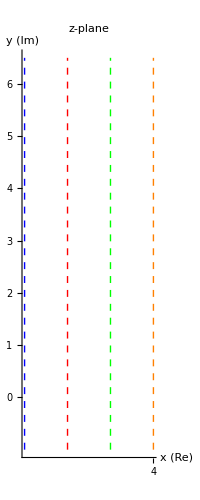
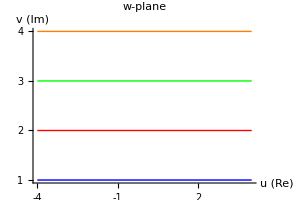

```mathematica
Row[{Graphics[{{Dashed,Blue,Line[{{1,-1},{1,6.5}}]},{Dashed,Red,Line[{{2,-1},{2,6.5}}]},{Dashed,Green,Line[{{3,-1},{3,6.5}}]},{Dashed,Orange,Line[{{4,-1},{4,6.5}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{5,-1},{-1,7}},Ticks->{{0,1,2,3,4,5,6,7},{0,1,2,3,4,5,6,7}},ImageSize->200,AxesLabel->{"x (Re)","y (Im)"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],Graphics[{{Blue,Line[{{4,1},{-4,1}}]},{Red,Line[{{4,2},{-4,2}}]},{Green,Line[{{4,3},{-4,3}}]},{Orange,Line[{{4,4},{-4,4}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{4.5,-4.5},{-1,4.5}},Ticks->{{-4,-3,-2,-1,0,1,2,3,4},{0,1,2,3,4}},ImageSize->300,AxesLabel->{"u (Re)","v (Im)"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]]  }]
```

with unrestricted y values stretching out the w-plane lines horizontally.

The y value cases, with y=k=const, are done similarly. In this case

```mathematica
yargot=Table[{u[x,k],v[x,k]},{k,1,4}]
```

{{-1-Im[x],Re[x]},{-2-Im[x],Re[x]},{-3-Im[x],Re[x]},{-4-Im[x],Re[x]}}

```mathematica
Simplify[yargot,Assumptions->x∈Reals]
```

{{-1,x},{-2,x},{-3,x},{-4,x}}

The above table gives the transformations for the z-values given in the constant y part of the problem. Plotted, they should look like

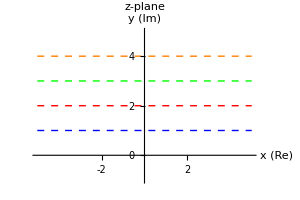
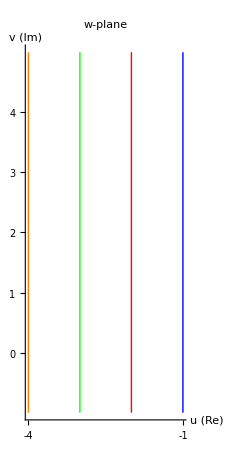

```mathematica
Row[{Graphics[{{Dashed,Blue,Line[{{-5,1},{5,1}}]},{Dashed,Red,Line[{{-5,2},{5,2}}]},{Dashed,Green,Line[{{-5,3},{5,3}}]},{Dashed,Orange,Line[{{-5,4},{5,4}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-5,5},{-1,5}},Ticks->{{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6},{0,1,2,3,4,5,6,7}},ImageSize->300,AxesLabel->{"x (Re)","y (Im)"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],Graphics[{{Blue,Line[{{-1,-1},{-1,5}}]},{Red,Line[{{-2,-1},{-2,5}}]},{Green,Line[{{-3,-1},{-3,5}}]},{Orange,Line[{{-4,-1},{-4,5}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{2,-4.5},{-1,5.5}},Ticks->{{-4,-3,-2,-1,0,1,2,3,4},{0,1,2,3,4}},ImageSize->230,AxesLabel->{"u (Re)","v (Im)"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]]  }]
```

with unrestricted x values stretching out the w-plane lines vertically.

9.  Translation. Curves as in problem 6, w = z + 2 + I

```mathematica
Clear["Global`*"]
```

Defining the mapping.

```mathematica
u[x_,y_]=Re[(x+ⅈ y)+2+ⅈ]
```

2-Im[y]+Re[x]

```mathematica
v[x_,y_]=Im[(x+ⅈ y)+2+ⅈ]
```

1+Im[x]+Re[y]

```mathematica
argot=Table[{u[c,y],v[c,y]},{c,1,4}]
```

{{3-Im[y],1+Re[y]},{4-Im[y],1+Re[y]},{5-Im[y],1+Re[y]},{6-Im[y],1+Re[y]}}

```mathematica
Simplify[argot,Assumptions->y∈Reals]
```

{{3,1+y},{4,1+y},{5,1+y},{6,1+y}}

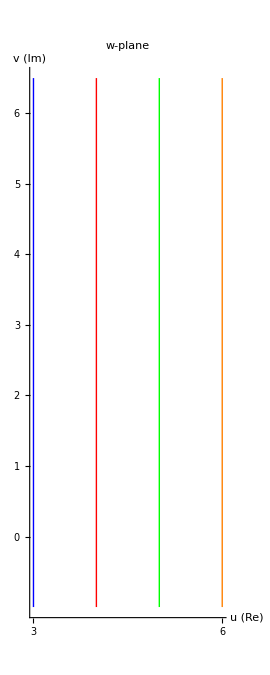
-Graphics--Graphics-

```mathematica
Row[{Graphics[{{Dashed,Blue,Line[{{1,-1},{1,6.5}}]},{Dashed,Red,Line[{{2,-1},{2,6.5}}]},{Dashed,Green,Line[{{3,-1},{3,6.5}}]},{Dashed,Orange,Line[{{4,-1},{4,6.5}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{5,-1},{-1,7}},Ticks->{{0,1,2,3,4,5,6,7},{0,1,2,3,4,5,6,7}},ImageSize->200,AxesLabel->{"x (Re)","y (Im)"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],Graphics[{{Blue,Line[{{3,-1},{3,6.5}}]},{Red,Line[{{4,-1},{4,6.5}}]},{Green,Line[{{5,-1},{5,6.5}}]},{Orange,Line[{{6,-1},{6,6.5}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{7.55,-1},{-1,7}},Ticks->{{0,1,2,3,4,5,6,7},{0,1,2,3,4,5,6,7}},ImageSize->270,AxesLabel->{"u (Re)","v (Im)"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]]  }]
```

Each point in the above graph is moved 2 units to the right and 1 unit up. Since y already cruises the length of the real axis, the vertical change goes unnoticed.

```mathematica
yargot=Table[{u[x,k],v[x,k]},{k,1,4}]
```

{{2+Re[x],2+Im[x]},{2+Re[x],3+Im[x]},{2+Re[x],4+Im[x]},{2+Re[x],5+Im[x]}}

```mathematica
Simplify[yargot,Assumptions->x∈Reals]
```

{{2+x,2},{2+x,3},{2+x,4},{2+x,5}}

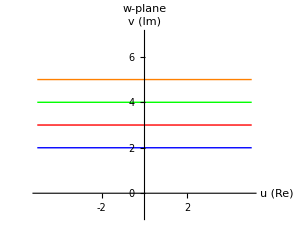
-Graphics--Graphics-

```mathematica
Row[{Graphics[{{Dashed,Blue,Line[{{-5,1},{5,1}}]},{Dashed,Red,Line[{{-5,2},{5,2}}]},{Dashed,Green,Line[{{-5,3},{5,3}}]},{Dashed,Orange,Line[{{-5,4},{5,4}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-5,5},{-1,5}},Ticks->{{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6},{0,1,2,3,4,5,6,7}},ImageSize->300,AxesLabel->{"x (Re)","y (Im)"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],Graphics[{{Blue,Line[{{-5,2},{5,2}}]},{Red,Line[{{-5,3},{5,3}}]},{Green,Line[{{-5,4},{5,4}}]},{Orange,Line[{{-5,5},{5,5}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{-5,5},{-1,7}},Ticks->{{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6},{0,1,2,3,4,5,6,7}},ImageSize->300,AxesLabel->{"u (Re)","v (Im)"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]]}]
```

Each point in the above graph is moved 2 units to the right and 1 unit up. Since x already travels the length of the real axis, the horizontal change goes unnoticed.

11 - 20 Mapping of regions
Sketch or graph the given region and its image under the given mapping.

11. Abs[z]≤1/2, -π/8<Arg[z]<π/8, w=z^2

```mathematica
Clear["Global`*"]
```

Tracing the influence of the transformation on the z-plane, I see that

```mathematica
Rⅇ^(ⅈ ϕ)==w==f[z]==f[r ⅇ^(ⅈ θ)]==z^2⌊_(z=r ⅇ^(ⅈ θ))==(r ⅇ^(ⅈ θ))^2==r^2(ⅇ^(ⅈ θ))^2==r^2 ⅇ^(ⅈ 2 θ)
```

In a nutshell, distances will be squared and angles doubled. The first part of the problem defines a circle, and the second part constrains the circle into a pie slice. The radius of the z-circle is 1/2, which when squared for the w-plane becomes 1/4. Meanwhile the arc of the z-slice is increased from (-π/8 min,π/8 max) up to w-slice (-π/4min, π/4max).

The sketch:

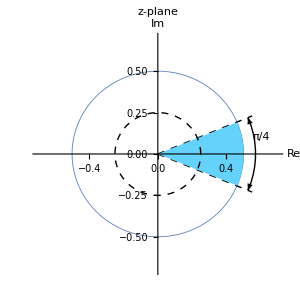
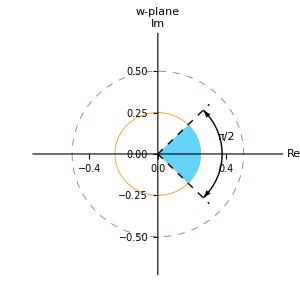

```mathematica
p1=ParametricPlot[{{1/2 Cos[t]+0,1/2 Sin[t]+0},{1/4 Cos[t]+0,1/4 Sin[t]+0}},{t,-π,π},ImageSize->300,PlotStyle->{{Dashed,Thickness[0.002]},{Thickness[0.002]}},Epilog->{{RGBColor[100/255,210/255,250/255],Disk[{0,0},1/4,{-π/4,π/4}]},{Dashed,Line[{{0,0},{0.3,0.3}}]},{Dashed,Line[{{0,0},{0.3,-0.3}}]},{Circle[{0,0},3/8,{-π/4,π/4}]},{Arrowheads[.025],Arrow[{{0.285,0.242},{0.27,0.26}}]},{Arrowheads[.025],Arrow[{{0.285,-0.242},{0.27,-0.26}}]},{Text["π/2",{0.4,0.1}]}},AxesLabel->{"Re","Im"},PlotRange->{-0.7,0.7},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]] ParametricPlot[{1/2 Cos[t]+0,1/2 Sin[t]+0},{t,-π,π},ImageSize->300,PlotStyle->{Thickness[0.002]},Epilog->{{Dashed,Line[{{0,0},{0.55,0.23}}]},{Dashed,Line[{{0,0},{0.55,-0.23}}]},{RGBColor[100/255,210/255,250/255],Disk[{0,0},1/2,{-π/8,π/8}]},{Dashed,Circle[{0,0},1/4,{0,2π}]},{Circle[{0,0},0.57,{-π/8,π/8}]},{Arrowheads[.025],Arrow[{{0.532,0.2},{0.525,0.22}}]},{Arrowheads[.025],Arrow[{{0.532,-0.2},{0.525,-0.22}}]},{Text["π/4",{0.605,0.1}]}},AxesLabel->{"Re","Im"},PlotRange->{-0.7,0.7},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]]
```

I see now that just using Graphics>Circle would have been a somewhat quicker effort than the ParametricPlot.

13.  2 ≤ Im[z] ≤ 5, w = I z

```mathematica
Clear["Global`*"]
```

Problem 7 told me that the mapping w=ⅈ z is a positive rotation of π/2. The mapping is the same in this problem,

```mathematica
u[x_,y_]=Re[ⅈ(x+ⅈ y)]
```

-Im[x]-Re[y]

```mathematica
v[x_,y_]=Im[ⅈ (x+ⅈ y)]
```

-Im[y]+Re[x]

The mapping will depend on the changes done to the boundary lines, so I will do them one at a time

```mathematica
{u[x,2],v[x,2]}
```

{-2-Im[x],Re[x]}

```mathematica
Simplify[%,Assumptions->x∈Reals]
```

{-2,x}

```mathematica
{u[x,5],v[x,5]}
```

{-5-Im[x],Re[x]}

```mathematica
Simplify[%,Assumptions->x∈Reals]
```

{-5,x}

The mapped boundary lines will be at u=-2,u=-5, and the w-points inside will be the new territory.

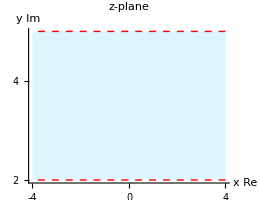
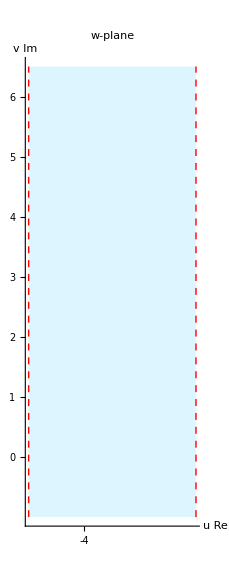

```mathematica
Row[{Graphics[{{RGBColor[220/255,245/255,255/255],Rectangle[{-4,2},{4,5}]},{Dashed,Red,Line[{{4,2},{-4,2}}]},{Dashed,Red,Line[{{4,5},{-4,5}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{4.5,-4.5},{-1,6.5}},Ticks->{{-4,-3,-2,-1,0,1,2,3,4,5,6},{0,1,2,3,4,5,6}},ImageSize->260,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]] ,
Graphics[{{RGBColor[220/255,245/255,255/255],Rectangle[{-5,-1},{-2,6.5}]},{Dashed,Red,Line[{{-2,-1},{-2,6.5}}]},{Dashed,Red,Line[{{-5,-1},{-5,6.5}}]}},Axes->True, AxesOrigin->{0,0},PlotRange->{{2,-6},{-1,6.5}},Ticks->{{-4,-3,-2,-1,0,1,2,3,4,5,6},{0,1,2,3,4,5,6}},ImageSize->230,AxesLabel->{"u Re","v Im"},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]] }]
```

15.  Abs[z-1/2]≤1/2, w=1/z

```mathematica
Clear["Global`*"]
```

The s.m. covers this problem, first noting that the circle equation can be manipulated

```mathematica
(x-1/2)^2+y^2==(1/2)^2⟹ x^2-x+1/4+y^2==1/4⟹ (x^2+y^2)-x==0
```

while also pulling in an expression incorporating the conjugate (found on p. 613 in numbered line (3))

```mathematica
x^2+y^2==Abs[z]^2==z z*
```

and noting that

```mathematica
x==(z+z*)/2
```

follows from the definition of the conjugate, the circle equation is recast as

```mathematica
z z*-(z+z*)/2==0
```

which is interesting, but which will not be pursued further.

Instead I will make use of the transformation mapping equations:

```mathematica
u[x_,y_]=Re[(x+ⅈ y)^-1]
```

Re[1/(x+ⅈ y)]

```mathematica
v[x_,y_]=Im[(x+ⅈ y)^-1]
```

Im[1/(x+ⅈ y)]

```mathematica
com[x_,y_]={u[x,y],v[x,y]}
```

{Re[1/(x+ⅈ y)],Im[1/(x+ⅈ y)]}

to calculate some resulting transformation mapping of some points in the circle, like the center (yellow).

```mathematica
u[1/2,0]
```

2

```mathematica
v[1/2,0]
```

0

The following cell shows the mapped circle will be stretched way out there on the u axis.

```mathematica
u[0.001,0]
```

1000.

I will work through the equivalence line. However, this is not really for application, just for interest.

```mathematica
Rⅇ^(ⅈ ϕ)==w==f[z]==f[r ⅇ^(ⅈ θ)]==z^-1⌊_(z=r ⅇ^(ⅈ θ))==(r ⅇ^(ⅈ θ))^-1==r^-1(ⅇ^(ⅈ θ))^-1==r^-1 ⅇ^(-ⅈ θ)
```

The below cell has a plot which doesn’t work, but I’m leaving it in anyway (the correct approach is in the cell after next). The problem is that the trig formatted circle formula causes problems when singularites are created by inverting it. It does show a illusory kind of promise, in that it presents the mapped circle outline, although accompanied with an extraneous curve and two illegal expression warnings.

Power::infy: Infinite expression 1/0. encountered.

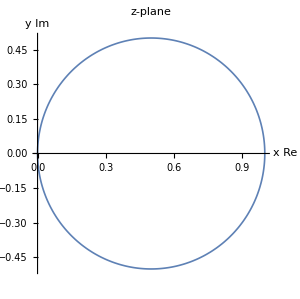
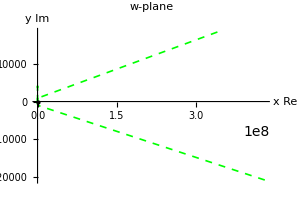

```mathematica
Row[{ParametricPlot[{(1/2 Cos[t]+1/2),(1/2 Sin[t])},{t,0,2π},ImageSize->300,PlotStyle->{Thickness[0.004]},Epilog->{},AxesLabel->{"x Re","y Im"},PlotRange->{{1.2,-0.1},{0.7,-0.7}},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[{(1/2 Cos[t]+1/2)^-1,(1/2 Sin[t])^-1},{t,-π,π},ImageSize->300,PlotStyle->{Green,Dashed,Thickness[0.004]},Epilog->{(*{RGBColor[220/255,245/255,255/255],Rectangle[{1.03,-1},{3,6.5}]},*){Point[{2,0}]}},AxesLabel->{"x Re","y Im"},PlotRange->{{5,-0.1},{5,-0.1}},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White](*,Exclusions->{t,π/2,-π/2,-π,2π,0}*)] }]
```

The below cell shows the format that works. This time the circle maps to a single line. By checking the center point of the mapped circle, calculated above in yellow cells, it can be seen on which side of the line the body of the circle falls.

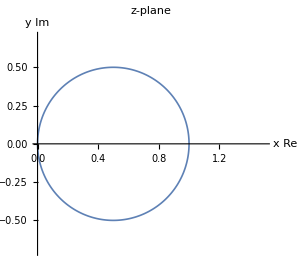
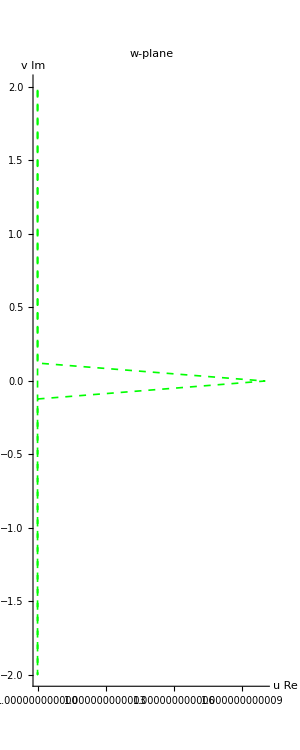

```mathematica
Row[{ParametricPlot[{(1/2 Cos[t]+1/2),(1/2 Sin[t])},{t,0,2π},ImageSize->300,PlotStyle->{Thickness[0.004]},Epilog->{},AxesLabel->{"x Re","y Im"},PlotRange->{{0,1.5},{-0.7,0.7}},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[{Re[(1/2 ⅇ^(ⅈ t)+1/2)^-1],Im[(1/2 ⅇ^(ⅈ t))^-1]},{t,0,2π},ImageSize->300,PlotStyle->{Green,Dashed,Thickness[0.004]},Epilog->{(*{RGBColor[220/255,245/255,255/255],Rectangle[{1.03,-2},{5,2}]},*){Point[{2,0}]}},AxesLabel->{"u Re","v Im"},PlotRange->{{5,-0.1},{3,-3}},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White]] }]
```

A rectangle in the above plot was to show the body of the mapped circle in the w-plane, but it was very inaccurate. The set of nested concentric circles below gives a better idea of the area covered by the mapped body.

```mathematica
pp1=ParametricPlot[{Re[(.1 ⅇ^(ⅈ t)+1/2)^-1],Im[(.1 ⅇ^(ⅈ t))^-1]},{t,0,2π},ImageSize->400,PlotRange->{{0,10},{-12,12}}, AspectRatio->0.6,PlotStyle->{Brown, Thickness[0.003]}];
```

```mathematica
pp2=ParametricPlot[{Re[(.2 ⅇ^(ⅈ t)+1/2)^-1],Im[(.2 ⅇ^(ⅈ t))^-1]},{t,0,2π},ImageSize->400,PlotStyle->{Orange, Thickness[0.003]}];
```

```mathematica
pp3=ParametricPlot[{Re[(.3 ⅇ^(ⅈ t)+1/2)^-1],Im[(.3 ⅇ^(ⅈ t))^-1]},{t,0,2π},ImageSize->400,PlotStyle->{Red, Thickness[0.003]}];
```

```mathematica
pp4=ParametricPlot[{Re[(.4 ⅇ^(ⅈ t)+1/2)^-1],Im[(.4 ⅇ^(ⅈ t))^-1]},{t,0,2π},ImageSize->400,PlotStyle->{Green, Thickness[0.003]}];
```

```mathematica
pp5=ParametricPlot[{Re[(.5 ⅇ^(ⅈ t)+1/2)^-1],Im[(.5 ⅇ^(ⅈ t))^-1]},{t,0,2π},ImageSize->400,PlotStyle->{Blue, Thickness[0.003]}];
```

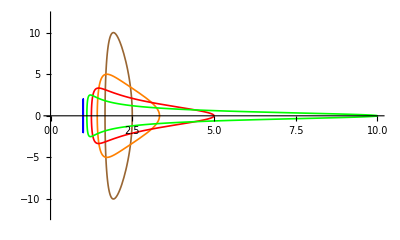

```mathematica
Show[pp1,pp2,pp3,pp4,pp5]
```

17.  -Log[2]≤x≤Log[4], w=ⅇ^z

```mathematica
Clear["Global`*"]
```

Doing a little log identity,

```mathematica
Log[1/2]≤x≤Log[4]
```

-Log[2]≤x≤Log[4]

As I understand it, the logarithm being a monotonically increasing function allows me to say

```mathematica
1/2≤ⅇ^x≤4
```

1/2≤ⅇ^x≤4

Meanwhile the little trick in numbered line (10) on p. 631 confers

Abs[ⅇ^z]==ⅇ^x

So that

1/2≤Abs[ⅇ^z]≤4 ⟹ 1/2≤Abs[w]≤4 by the problem description. So in the w-plane it becomes an annulus, with the radii of the two circles being 1/2 and 4.

```mathematica
N[-Log[2]]
```

-0.693147

```mathematica
N[Log[4]]
```

1.38629

```mathematica
rangein=Range[-.69,1.38,0.15]
```

{-0.69,-0.54,-0.39,-0.24,-0.09,0.06,0.21,0.36,0.51,0.66,0.81,0.96,1.11,1.26}

```mathematica
Table[{ⅇ^n},{n,{-0.69,-0.5399999999999999,-0.38999999999999996,-0.24,-0.08999999999999997,0.06000000000000005,0.20999999999999996,0.3600000000000001,0.51,0.6599999999999999,0.81,0.96,1.1099999999999999,1.26,1.38}}];
```

```mathematica
Flatten[%];
```

```mathematica
color1=RGBColor[210/255,210/255,100/255];color2=RGBColor[10/255,160/255,50/255];
color3=RGBColor[200/255,30/255,250/255];color4=RGBColor[120/255,220/255,220/255];
color5=RGBColor[200/255,22/255,22/255];color6=RGBColor[100/255,100/255,240/255];
color7=RGBColor[240/255,240/255,50/255];color8=RGBColor[160/255,30/255,160/255];
color9=RGBColor[40/255,100/255,180/255];color10=RGBColor[250/255,180/255,180/255];
```

The annulus in the w-plane is a single, undivided annulus, but I thought it would be interesting to see the contributions from various radii in the circle in the z-plane.

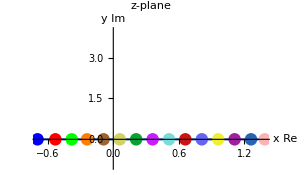
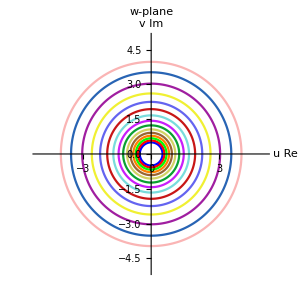

```mathematica
Row[{p1=Plot[0,{p,-0.6931,1.3862},PlotRange->{{-0.693,1.386},{-1,4}},PlotStyle->{Thickness[0.006]},Epilog->{{Blue,PointSize[0.03],Point[{-0.693,0}]},{Red,PointSize[0.03],Point[{-0.53,0}]},{Green,PointSize[0.03],Point[{-0.38,0}]},{Orange,PointSize[0.03],Point[{-0.24,0}]},{Brown,PointSize[0.03],Point[{-0.089,0}]},{color1,PointSize[0.03],Point[{0.06,0}]},{color2,PointSize[0.03],Point[{0.209,0}]},{color3,PointSize[0.03],Point[{0.36,0}]},{color4,PointSize[0.03],Point[{0.51,0}]},
{color5,PointSize[0.03],Point[{0.659,0}]},
{color6,PointSize[0.03],Point[{0.81,0}]},
{color7,PointSize[0.03],Point[{0.96,0}]},
{color8,PointSize[0.03],Point[{1.11,0}]},
{color9,PointSize[0.03],Point[{1.26,0}]},{color10,PointSize[0.03],Point[{1.386,0}]}},ImageSize->300,AxesLabel->{"x Re","y Im"},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White]],ParametricPlot[Evaluate[Table[{ Re[(n ⅇ^(ⅈ t))],Im[n ⅇ^(ⅈ t)]},{n,{0.501,0.582,0.677,0.786,0.913,1.061,1.233,1.433,1.665,1.934,2.247,2.611,3.034,3.525,3.974}}]],{t,0,2π},ImageSize->300,AxesLabel->{"u Re","v Im"},PlotRange->{{-5,5},{-5,5}},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White],PlotStyle->{{Blue},{Red},{Green},{Orange},{Brown},{color1},{color2},{color3},{color4},{color5},{color6},{color7},{color8},{color9},{color10}}]}]
```

19.  1<Abs[z]<4, π/4<θ≤(3 π)/4, w=Log[z]

```mathematica
Clear["Global`*"]
```

Tracing the influence of the mapping transformation on the z-plane, I see that

```mathematica
Rⅇ^(ⅈ ϕ)==w==f[z]==f[r ⅇ^(ⅈ θ)]==Log[z]⌊_(z=r ⅇ^(ⅈ θ))==Log[r ⅇ^(ⅈ θ)]==Log[r]+Log[ⅇ^(ⅈ θ)]==Log[r]+ ⅈ θ
```

and proceed to insert it directly into plot commands. In the z-plot I don’t bother to show radial boundary lines this time.

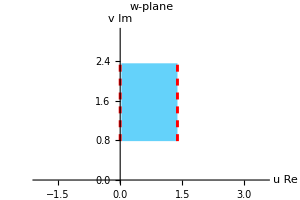
-Graphics--Graphics-

```mathematica
Row[{ParametricPlot[Evaluate[Table[{ Re[(n ⅇ^(ⅈ t))],Im[n ⅇ^(ⅈ t)]},{n,{1,4}}]],{t,0,2π},ImageSize->300,AxesLabel->{"x Re","y Im"},PlotRange->{{-5,5},{-5,5}},PlotLabel->Style[Framed[  "  z-plane "],10,Blue,Background->White],Epilog->{{RGBColor[100/255,210/255,250/255],Annulus[{0,0},{1,4},{π/4,(3π)/4}]}}],ParametricPlot[Evaluate[Table[{ Re[(Log[r]+ ⅈ θ)],Im[Log[r]+ ⅈ θ]},{r,{1,4}}]],{θ,π/4,(3π)/4},ImageSize->300,AxesLabel->{"u Re","v Im"},PlotRange->{{-2,3.5},{0,3}},PlotStyle->{{Red,Dashed,Thickness[0.007]},{Red,Dashed,Thickness[0.007]}},PlotLabel->Style[Framed[  "  w-plane "],10,Red,Background->White],Epilog->{{RGBColor[100/255,210/255,250/255],Rectangle[{0.03,π/4},{Log[4],(3π)/4}]}}]}]
```

21 - 26 Failure of conformity
Find all points at which the mapping is not conformal.

21.  A cubic polynomial

```mathematica
Clear["Global`*"]
```

As prompted by the s.m. a general cubic polynomial looks like

```mathematica
gcubp=Subscript[a, 3] z^3+Subscript[a, 2] z^2+Subscript[a, 1] z+Subscript[a, 0]
```

a_0+z a_1+z^2 a_2+z^3 a_3

First get the derivative

```mathematica
inter=D[gcubp,{z}]
```

a_1+2 z a_2+3 z^2 a_3

Then solve this for roots

```mathematica
Solve[inter==0,{z}]
```

{{z→(-a_2-√(a_2^2-3 a_1 a_3))/(3 a_3)},{z→(-a_2+√(a_2^2-3 a_1 a_3))/(3 a_3)}}

The above notation is according to the s.m., which is not the same as the text. Using the text notation,

```mathematica
gcubt=z^3+a z^2+b z+c
```

c+b z+a z^2+z^3

```mathematica
tinter=D[gcubt,{z}]
```

b+2 a z+3 z^2

```mathematica
Solve[tinter==0,z]
```

{{z→1/3 (-a-√(a^2-3 b))},{z→1/3 (-a+√(a^2-3 b))}}

The above roots make the derivative equal to zero, and that is what constitutes nonconformality.

23.  (z+1/2)/(4 z^2+2)

```mathematica
Clear["Global`*"]
```

```mathematica
yeeha=(z+1/2)/(4 z^2+2)
```

(1/2+z)/(2+4 z^2)

```mathematica
yeehaD=D[yeeha,{z}]
```

-(8 z (1/2+z))/((2+4 z^2)^2)+1/(2+4 z^2)

```mathematica
Together[yeehaD]
```

(1-2 z-2 z^2)/(2 (1+2 z^2)^2)

```mathematica
Solve[1-2 z-2 z^2==0,z]
```

{{z→1/2 (-1-√3)},{z→1/2 (-1+√3)}}

The above green cell matches the text answer in content, as demonstrated by the following two cells.

```mathematica
PossibleZeroQ[(-1+√3)/2-1/2 (-1+√3)]
```

True

```mathematica
PossibleZeroQ[(-1-√3)/2-1/2 (-1-√3)]
```

True

25.  Cosh[z]

```mathematica
Clear["Global`*"]
```

```mathematica
coshD=D[Cosh[z],{z}]
```

Sinh[z]

```mathematica
Solve[coshD==0,z]
```

{{z→ConditionalExpression[2 ⅈ π C[1],C[1]∈Integers]},{z→ConditionalExpression[ⅈ π+2 ⅈ π C[1],C[1]∈Integers]}}

The above green cell constant C[1] offers enough flexibility to match all the answers in the text.

29 - 35 Magnification ratio, Jacobian
Find the magnification ratio, M. Describe what it tells you about the mapping. Where is M=1? Find the Jacobian J.

29.  w=1/2 z^2

```mathematica
Clear["Global`*"]
```

Examining the Magnification ratio amounts to looking at the absolute value of the first derivative.

```mathematica
f[z_]=1/2 z^2
```

z^2/2

```mathematica
mdog=D[f[z],{z}]
```

z

The cell below tells me that magnification equals 1 on the unit circle,

```mathematica
ComplexExpand[Abs[x+ⅈ y]]
```

√(x^2+y^2)

The grid below shows some points close to the origin along with the resulting magnification there.

```mathematica
Grid[Table[{x,y,√(x^2+y^2)},{x,-2,2},{y,-2,2}],Frame->All]
```

{-2,-2,2 √2} | {-2,-1,√5} | {-2,0,2} | {-2,1,√5} | {-2,2,2 √2}
{-1,-2,√5} | {-1,-1,√2} | {-1,0,1} | {-1,1,√2} | {-1,2,√5}
{0,-2,2} | {0,-1,1} | {0,0,0} | {0,1,1} | {0,2,2}
{1,-2,√5} | {1,-1,√2} | {1,0,1} | {1,1,√2} | {1,2,√5}
{2,-2,2 √2} | {2,-1,√5} | {2,0,2} | {2,1,√5} | {2,2,2 √2}

The Jacobian, according to numbered line (5) on p. 741, is

```mathematica
Abs[f'[z]]^2
```

Abs[z]^2

31.  w=1/z

```mathematica
Clear["Global`*"]
```

```mathematica
f[z_]=1/z
```

1/z

The expression for the Magnification ratio M is

```mathematica
Abs[D[f[z],{z}]]
```

1/Abs[z]^2

```mathematica
ComplexExpand[1/Abs[x+ⅈ y]^2]
```

1/(x^2+y^2)

As the cell below shows, the magnification is equal to 1 on the unit circle.

```mathematica
tes[x_,y_]=1/(x^2+y^2)
```

1/(x^2+y^2)

The concept of Magnification concerns what the absolute value of the derivative may do to various z_0 values. Again, taking integers, the following grid shows what magnifications result from various x and y values around the origin.

```mathematica
Grid[Table[{x,y,tes[x,y]},{x,-2,2},{y,-2,2}],Frame->All]
```

Power::infy: Infinite expression 1/0 encountered.

{-2,-2,1/8} | {-2,-1,1/5} | {-2,0,1/4} | {-2,1,1/5} | {-2,2,1/8}
{-1,-2,1/5} | {-1,-1,1/2} | {-1,0,1} | {-1,1,1/2} | {-1,2,1/5}
{0,-2,1/4} | {0,-1,1} | {0,0,ComplexInfinity} | {0,1,1} | {0,2,1/4}
{1,-2,1/5} | {1,-1,1/2} | {1,0,1} | {1,1,1/2} | {1,2,1/5}
{2,-2,1/8} | {2,-1,1/5} | {2,0,1/4} | {2,1,1/5} | {2,2,1/8}

And the Jacobian is equal to

```mathematica
(1/Abs[z]^2)^2
```

1/Abs[z]^4

33. w=e^z

```mathematica
Clear["Global`*"]
```

```mathematica
f[z]=ⅇ^z
```

ⅇ^z

The cell below shows that the magnification is 1 wherever z=0; as the y value is not involved, this means that the entire y-axis has a magnification of 1.

```mathematica
Abs[D[f[z],{z}]]
```

ⅇ^Re[z]

The above factor is equal to ⅇ^x. To see some examples of the magnification around the origin, look at

```mathematica
Grid[Table[{x,y,ⅇ^x},{x,-2,2},{y,-2,2}],Frame->All]
```

{-2,-2,1/ⅇ^2} | {-2,-1,1/ⅇ^2} | {-2,0,1/ⅇ^2} | {-2,1,1/ⅇ^2} | {-2,2,1/ⅇ^2}
{-1,-2,1/ⅇ} | {-1,-1,1/ⅇ} | {-1,0,1/ⅇ} | {-1,1,1/ⅇ} | {-1,2,1/ⅇ}
{0,-2,1} | {0,-1,1} | {0,0,1} | {0,1,1} | {0,2,1}
{1,-2,ⅇ} | {1,-1,ⅇ} | {1,0,ⅇ} | {1,1,ⅇ} | {1,2,ⅇ}
{2,-2,ⅇ^2} | {2,-1,ⅇ^2} | {2,0,ⅇ^2} | {2,1,ⅇ^2} | {2,2,ⅇ^2}

As for the Jacobian,

```mathematica
(ⅇ^x)^2
```

ⅇ^(2 x)

35. w = Log[z]

```mathematica
Clear["Global`*"]
```

```mathematica
f[z_]=Log[z]
```

Log[z]

As the cell below testifies, and the grid corroborates, the magnification equals 1 on the unit circle.

```mathematica
Abs[D[f[z],{z}]]
```

1/Abs[z]

```mathematica
Grid[Table[{x,y,1/Abs[x+ⅈ y]},{x,-2,2},{y,-2,2}],Frame->All]
```

Power::infy: Infinite expression 1/0 encountered.

{-2,-2,1/(2 √2)} | {-2,-1,1/(√5)} | {-2,0,1/2} | {-2,1,1/(√5)} | {-2,2,1/(2 √2)}
{-1,-2,1/(√5)} | {-1,-1,1/(√2)} | {-1,0,1} | {-1,1,1/(√2)} | {-1,2,1/(√5)}
{0,-2,1/2} | {0,-1,1} | {0,0,ComplexInfinity} | {0,1,1} | {0,2,1/2}
{1,-2,1/(√5)} | {1,-1,1/(√2)} | {1,0,1} | {1,1,1/(√2)} | {1,2,1/(√5)}
{2,-2,1/(2 √2)} | {2,-1,1/(√5)} | {2,0,1/2} | {2,1,1/(√5)} | {2,2,1/(2 √2)}

As for the Jacobian,

```mathematica
(1/Abs[z])^2
```

1/Abs[z]^2